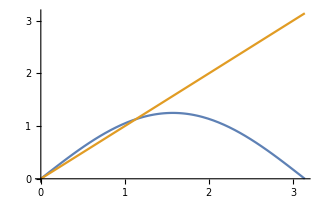

```mathematica
Plot[{1/0.8 Sin[θ],1θ},{θ,0,π}]
```

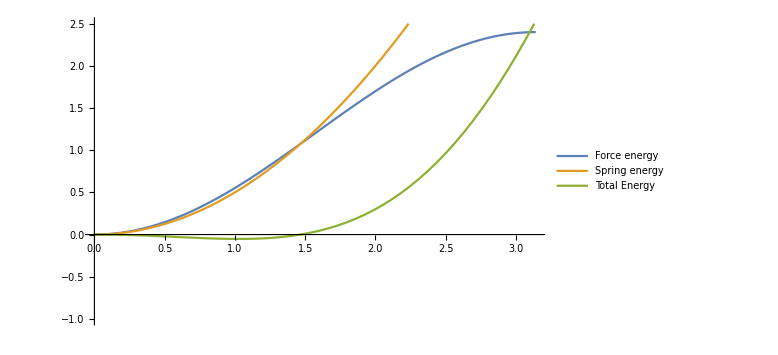

```mathematica
Block[{P=1.2,l=1,k=1},
Π1[θ_]:=-P l(1-Cos[θ]);
Π2[θ_]:=1/2 k θ^2;
Plot[{-Π1[θ],Π2[θ],Π1[θ]+Π2[θ]},{θ,0,π},PlotRange->{{0,π},{-1,2.5}},PlotLegends->{"Force energy","Spring energy","Total Energy"},ImageSize->Large]]
```